```mathematica
ClearAll[E1,Sfunc,A,DsFunc,plotE1,tValues,p,t,newResults,generatePlotAndRoots];

(*Define the electric field function*)
E1[t_]:=Cos[Pi/4] Cos[t]-Sin[Pi/4] Cos[2t];
A[tx_]=-Integrate[E1[t],t]/. t->tx;

(*Function to generate plots and roots for a given p*)
generatePlotAndRoots[p_]:=
Module[
{Ip=0.5,Sf,Sfunc,DsFunc,realMin,realMax,imagMin,imagMax,realSteps,imagSteps,listofseeds,allSolutions,complexSolutions,nonrepeatedSolutions,tValues,tolerance,filteredTValues,plotE1,plotRoots},

(*Define Sf,Sfunc,and DsFunc in x and y*)
Sf[tk_]=Integrate[2 p*A[t]+(A[t])^2,t]/. t->tk;
Sfunc[t_]:=0.5*Sf[t]+(0.5*p^2+Ip)*t;
DsFunc[t_]:=D[Sfunc[tc],tc]/. tc->t;


(*Generate the grid of seeds*)
realMin=-2.133;realMax=4.15;
imagMin=0;imagMax=3;
realSteps=10;imagSteps=5;
listofseeds=Flatten[
Table[
x+I y,{x,realMin,realMax,(realMax-realMin)/realSteps},{y,imagMin,imagMax,(imagMax-imagMin)/imagSteps}
],1];

(*Find roots*)
allSolutions=Round[t/. Quiet[
Table[
FindRoot[DsFunc[t]==0,{t,tseed}],
{tseed,listofseeds}]
],0.0001];

complexSolutions=Select[allSolutions,Im[#]>0&];
nonrepeatedSolutions=DeleteDuplicates[complexSolutions];
tValues=SortBy[Select[nonrepeatedSolutions,(Re[#]>=realMin&&Re[#]<=realMax)&],Re[#]&];

(*Define a tolerance for considering values as 0*)
tolerance=10^-3;
filteredTValues=Select[tValues,Abs[Re[DsFunc[#]]]<=tolerance&&Abs[Im[DsFunc[#]]]<=tolerance&];

(*Plot E1 and the roots*)
plotE1=Quiet[
Plot[
E1[t],
{t,realMin,realMax},

PlotLabel->"p = "<>ToString[p],
AxesLabel->{"Time, t","Electric Field"},
ImageSize-> Large]
];

plotRoots=Quiet[
ListPlot[
{{Re[#],E1[Re[#]]}&/@filteredTValues},

PlotStyle->{Red,PointSize[0.02]},
AxesLabel->{"Time, t","Electric Field"},
ImageSize-> Large
]
];

(*Return both the plot and filteredTValues*)
{Show[plotE1,plotRoots,PlotRange->All],filteredTValues}];

(*Electric field plot along with saddle points as red dots,and for the slider for p from-3 to 3.*)
Manipulate[
Module[
{plotData,plotE1,plotRoots,filteredTValues},
plotData=generatePlotAndRoots[p];
plotE1=plotData[[1]];
filteredTValues=plotData[[2]];

plotRoots=ListPlot[
{{Re[#],E1[Re[#]]}&/@filteredTValues},

PlotStyle->{Red,PointSize[0.02]},
AxesLabel->{"Time, t","Electric Field"},
ImageSize-> Large
];

Show[plotE1,plotRoots,PlotRange->All]
],
{{p,0,"Momentum p"},-3,3,0.1} 
]
```

{{-2.0008,1.2825,-3.},{0.4965,1.6343,-3.},{0.7616,1.589,-3.},{3.8842,1.2373,-3.},{-1.9913,1.2652,-2.9},{0.4907,1.6225,-2.9},{0.7634,1.5754,-2.9},{3.8789,1.218,-2.9},{-1.9812,1.2474,-2.8},{0.4845,1.6106,-2.8},{0.7652,1.5613,-2.8},{3.873,1.1981,-2.8},{-1.9704,1.2292,-2.7},{0.478,1.5984,-2.7},{0.7673,1.5469,-2.7},{3.8666,1.1776,-2.7},{-1.9588,1.2104,-2.6},{0.4712,1.5859,-2.6},{0.7695,1.532,-2.6},{3.8597,1.1565,-2.6},{-1.9464,1.1911,-2.5},{0.464,1.5731,-2.5},{0.7719,1.5166,-2.5},{3.852,1.1346,-2.5},{-1.933,1.1714,-2.4},{0.4564,1.5601,-2.4},{0.7745,1.5008,-2.4},{3.8437,1.1121,-2.4},{-1.9186,1.1511,-2.3},{0.4484,1.5468,-2.3},{0.7774,1.4844,-2.3},{3.8344,1.0888,-2.3},{-1.9031,1.1304,-2.2},{0.4399,1.5332,-2.2},{0.7806,1.4675,-2.2},{3.8243,1.0648,-2.2},{-1.8863,1.1092,-2.1},{0.4308,1.5193,-2.1},{0.7841,1.4501,-2.1},{3.813,1.04,-2.1},{-1.8681,1.0876,-2.},{0.4212,1.5051,-2.},{0.7879,1.432,-2.},{3.8006,1.0145,-2.},{-1.8483,1.0656,-1.9},{0.411,1.4906,-1.9},{0.7921,1.4133,-1.9},{3.7868,0.9883,-1.9},{-1.8268,1.0433,-1.8},{0.4001,1.4758,-1.8},{0.7968,1.3939,-1.8},{3.7715,0.9614,-1.8},{-1.8033,1.0209,-1.7},{0.3884,1.4608,-1.7},{0.802,1.3737,-1.7},{3.7545,0.9339,-1.7},{-1.7777,0.9985,-1.6},{0.376,1.4455,-1.6},{0.8078,1.3529,-1.6},{3.7355,0.9059,-1.6},{-1.7498,0.9764,-1.5},{0.3626,1.43,-1.5},{0.8143,1.3312,-1.5},{3.7145,0.8776,-1.5},{-1.7194,0.9547,-1.4},{0.3483,1.4142,-1.4},{0.8215,1.3086,-1.4},{3.6912,0.8491,-1.4},{-1.6863,0.934,-1.3},{0.3329,1.3984,-1.3},{0.8297,1.2852,-1.3},{3.6654,0.8208,-1.3},{-1.6505,0.9145,-1.2},{0.3163,1.3824,-1.2},{0.8388,1.2609,-1.2},{3.637,0.793,-1.2},{-1.612,0.8968,-1.1},{0.2984,1.3664,-1.1},{0.8492,1.2356,-1.1},{3.606,0.766,-1.1},{-1.5708,0.8814,-1.},{0.2791,1.3506,-1.},{0.8609,1.2094,-1.},{3.5724,0.7402,-1.},{-1.5272,0.8687,-0.9},{0.2583,1.335,-0.9},{0.8743,1.1824,-0.9},{3.5362,0.716,-0.9},{-1.4815,0.8593,-0.8},{0.2359,1.3199,-0.8},{0.8894,1.1544,-0.8},{3.4978,0.6938,-0.8},{-1.4342,0.8535,-0.7},{0.2118,1.3054,-0.7},{0.9067,1.1257,-0.7},{3.4573,0.6738,-0.7},{-1.3858,0.8517,-0.6},{0.186,1.2919,-0.6},{0.9263,1.0964,-0.6},{3.4151,0.6563,-0.6},{-1.3369,0.8542,-0.5},{0.1584,1.2796,-0.5},{0.9487,1.0668,-0.5},{3.3714,0.6414,-0.5},{-1.2882,0.8609,-0.4},{0.1292,1.2688,-0.4},{0.974,1.0371,-0.4},{3.3267,0.6292,-0.4},{-1.2403,0.8719,-0.3},{0.0984,1.26,-0.3},{1.0024,1.0078,-0.3},{3.2811,0.6197,-0.3},{-1.1939,0.8869,-0.2},{0.0664,1.2533,-0.2},{1.0343,0.9794,-0.2},{3.2349,0.613,-0.2},{-1.1497,0.9057,-0.1},{0.0334,1.2493,-0.1},{1.0695,0.9525,-0.1},{3.1883,0.6089,-0.1},{-1.1081,0.9277,0.},{0.,1.2479,0.},{1.1081,0.9277,0.},{3.1416,0.6076,0.},{-1.0695,0.9525,0.1},{-0.0334,1.2493,0.1},{1.1497,0.9057,0.1},{3.0949,0.6089,0.1},{-1.0343,0.9794,0.2},{-0.0664,1.2533,0.2},{1.1939,0.8869,0.2},{3.0483,0.613,0.2},{-1.0024,1.0078,0.3},{-0.0984,1.26,0.3},{1.2403,0.8719,0.3},{3.0021,0.6197,0.3},{-0.974,1.0371,0.4},{-0.1292,1.2688,0.4},{1.2882,0.8609,0.4},{2.9565,0.6292,0.4},{-0.9487,1.0668,0.5},{-0.1584,1.2796,0.5},{1.3369,0.8542,0.5},{2.9118,0.6414,0.5},{-0.9263,1.0964,0.6},{-0.186,1.2919,0.6},{1.3858,0.8517,0.6},{2.8681,0.6563,0.6},{-0.9067,1.1257,0.7},{-0.2118,1.3054,0.7},{1.4342,0.8535,0.7},{2.8259,0.6738,0.7},{-0.8894,1.1544,0.8},{-0.2359,1.3199,0.8},{1.4815,0.8593,0.8},{2.7854,0.6938,0.8},{-0.8743,1.1824,0.9},{-0.2583,1.335,0.9},{1.5272,0.8687,0.9},{2.7469,0.716,0.9},{-0.8609,1.2094,1.},{-0.2791,1.3506,1.},{1.5708,0.8814,1.},{2.7108,0.7402,1.},{-0.8492,1.2356,1.1},{-0.2984,1.3664,1.1},{1.612,0.8968,1.1},{2.6772,0.766,1.1},{-0.8388,1.2609,1.2},{-0.3163,1.3824,1.2},{1.6505,0.9145,1.2},{2.6462,0.793,1.2},{-0.8297,1.2852,1.3},{-0.3329,1.3984,1.3},{1.6863,0.934,1.3},{2.6178,0.8208,1.3},{-0.8215,1.3086,1.4},{-0.3483,1.4142,1.4},{1.7194,0.9547,1.4},{2.592,0.8491,1.4},{-0.8143,1.3312,1.5},{-0.3626,1.43,1.5},{1.7498,0.9764,1.5},{2.5687,0.8776,1.5},{-0.8078,1.3529,1.6},{-0.376,1.4455,1.6},{1.7777,0.9985,1.6},{2.5477,0.9059,1.6},{-0.802,1.3737,1.7},{-0.3884,1.4608,1.7},{1.8033,1.0209,1.7},{2.5287,0.9339,1.7},{-0.7968,1.3939,1.8},{-0.4001,1.4758,1.8},{1.8268,1.0433,1.8},{2.5117,0.9614,1.8},{-0.7921,1.4133,1.9},{-0.411,1.4906,1.9},{1.8483,1.0656,1.9},{2.4964,0.9883,1.9},{-0.7879,1.432,2.},{-0.4212,1.5051,2.},{1.8681,1.0876,2.},{2.4826,1.0145,2.},{-0.7841,1.4501,2.1},{-0.4308,1.5193,2.1},{1.8863,1.1092,2.1},{2.4701,1.04,2.1},{-0.7806,1.4675,2.2},{-0.4399,1.5332,2.2},{1.9031,1.1304,2.2},{2.4589,1.0648,2.2},{-0.7774,1.4844,2.3},{-0.4484,1.5468,2.3},{1.9186,1.1511,2.3},{2.4487,1.0888,2.3},{-0.7745,1.5008,2.4},{-0.4564,1.5601,2.4},{1.933,1.1714,2.4},{2.4395,1.1121,2.4},{-0.7719,1.5166,2.5},{-0.464,1.5731,2.5},{1.9464,1.1911,2.5},{2.4311,1.1346,2.5},{-0.7695,1.532,2.6},{-0.4712,1.5859,2.6},{1.9588,1.2104,2.6},{2.4235,1.1565,2.6},{-0.7673,1.5469,2.7},{-0.478,1.5984,2.7},{1.9704,1.2292,2.7},{2.4165,1.1776,2.7},{-0.7652,1.5613,2.8},{-0.4845,1.6106,2.8},{1.9812,1.2474,2.8},{2.4102,1.1981,2.8},{-0.7634,1.5754,2.9},{-0.4907,1.6225,2.9},{1.9913,1.2652,2.9},{2.4043,1.218,2.9},{-0.7616,1.589,3.},{-0.4965,1.6343,3.},{2.0008,1.2825,3.},{2.3989,1.2373,3.}}

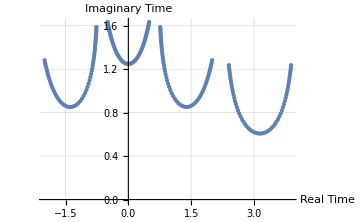

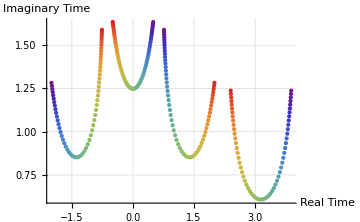

```mathematica
ClearAll[pValues,newResults,results,newTuple,tsExtended,validData,realAndImagTimes,colorFunction,coloredPoints];

pValues=Range[-3,3,0.1];

(*Generate results using the precise pValues*)
(*graph 1st term and list of saddle poinits second term*)
results=Table[
generatePlotAndRoots[p],{p,pValues}
];


newResults=Table[
{pValue=-3+(i-1)*0.1,results[[i,2]]},
{i,Length[results]}
];

tsExtended=Map[
Join[
{#[[1]]},PadRight[#[[2]],4,Null]
]&,newResults];

(*Filter and prepare the data for further processing*)
validData=Select[
Flatten[
Table[
If[
tsExtended[[i,j+1]]=!=Null,
{Re[tsExtended[[i,j+1]]],Im[tsExtended[[i,j+1]]],tsExtended[[i,1]]},
Nothing],
{i,Length[tsExtended]},
{j,1,4}]
,1],
#[[1]]=!=Null&]

(*Extract real and imaginary times*)
realAndImagTimes=validData[[All,1;;2]];

(*Plot the 2D graph*)
ListPlot[
realAndImagTimes,

AxesLabel->{"Real Time","Imaginary Time"},
PlotStyle->PointSize[Medium],
GridLines->Automatic,
ImageSize->Medium]


colorFunction[p_]:=ColorData["Rainbow"][Rescale[p,{-3,3}]]


(*Generate a list of colored points with the custom color function*)
coloredPoints=Table[
{colorFunction[validData[[i,3]]]
,Point[validData[[i,1;;2]]]
},
{i,1,Length[validData]}
];

(*Plot the 2D graph with the custom color grading for momentum*)
Show[
Graphics[
{coloredPoints},

Axes->True,
AxesLabel->{"Real Time","Imaginary Time"},
GridLines->Automatic],
PlotRange->All,
ImageSize->Medium,
AspectRatio->1/GoldenRatio]
```

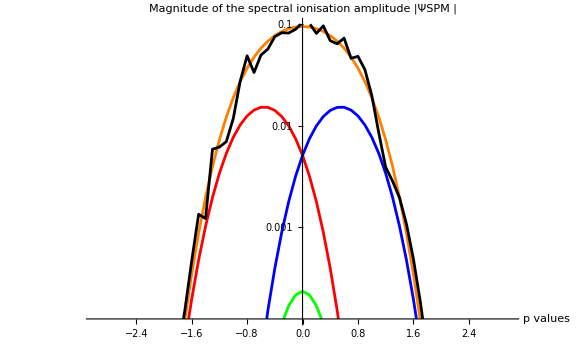

```mathematica
ClearAll[E1,Sf,Sfunc,A,DsFunc,D2sFunc,p,t,action,timeA, timeB, timeC, timeD, psiA, Ip, prefactor, pValues];

Ip = 0.5;
prefactor = (ⅈ / Sqrt[π])*(2*Ip)^(1/4);

(*Define the electric field function*)
E1[t_]:=Cos[Pi/4] Cos[t]-Sin[Pi/4] Cos[2t];
A[tx_]=-Integrate[E1[t],t]/. t->tx;

(*Define Sf,Sfunc,and DsFunc, D2sFunc, and e^iaction*)
Sf[p_,ty_]=Integrate[2 p*A[t]+(A[t])^2,t]/. t->ty;
Sfunc[p_,t_]:=0.5*Sf[p,t]+(0.5*p^2+Ip)*t;
DsFunc[p_,t_]:=D[Sfunc[p,tz],tz]/. tz->t;
D2sFunc[p_,t_]:=0.057*D[Sfunc[p,tz],{tz,2}]/. tz->t;
action[p_,t_] :=Exp[ⅈ*Sfunc[p,t]/0.057];

(*selects time saddle point solutions for trajectory A*)
timeA=
Table[
validData[[i]],
{i,1,Length[validData],4}
];
(*selects time saddle point solutions for trajectory B*)
timeB=
Table[
validData[[i]],
{i,2,Length[validData],4}
];
(*selects time saddle point solutions for trajectory C*)
timeC=
Table[
validData[[i]],
{i,3,Length[validData],4}
];
(*selects time saddle point solutions for trajectory D*)
timeD=
Table[
validData[[i]],
{i,4,Length[validData],4}
];
(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj A*)
psiA =Table[
prefactor*action[
timeA[[i,3]],
timeA[[i,1]]+ⅈ*timeA[[i,2]]
]*Sqrt[2π/(ⅈ *D2sFunc[
timeA[[i,3]],
timeA[[i,1]]+ⅈ*timeA[[i,2]]
])
],
{i,1,Length[timeA]}
];
(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj B*)
psiB =Table[
prefactor*action[
timeB[[i,3]],
timeB[[i,1]]+ⅈ*timeB[[i,2]]
]*Sqrt[2π/(ⅈ *D2sFunc[
timeB[[i,3]],
timeB[[i,1]]+ⅈ*timeB[[i,2]]
])
],
{i,1,Length[timeB]}
];
(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj C*)
psiC =Table[
prefactor*action[
timeC[[i,3]],
timeC[[i,1]]+ⅈ*timeC[[i,2]]
]*Sqrt[2π/(ⅈ *D2sFunc[
timeC[[i,3]],
timeC[[i,1]]+ⅈ*timeC[[i,2]]
])
],
{i,1,Length[timeC]}
];
(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj D*)
psiD =Table[
prefactor*action[
timeD[[i,3]],
timeD[[i,1]]+ⅈ*timeD[[i,2]]
]*Sqrt[2π/(ⅈ *D2sFunc[
timeD[[i,3]],
timeD[[i,1]]+ⅈ*timeD[[i,2]]
])
],
{i,1,Length[timeD]}
];
(*calculates the Magnitude of the spectral ionisation amplitude |ΨSPM | for Traj A+B+C+D*)
totalPsi =psiA+psiB +psiC +psiD;

(*defines pValues range from -3 to 3 in increments of 0.1*)
pValues=Range[-3,3,0.1];

(*creates the plots for Magnitude of the spectral ionisation amplitude |ΨSPM |for corresponding p values*)
ListLinePlot[
{Transpose[{pValues,Abs[psiA]}],Transpose[{pValues,Abs[psiB]}],Transpose[{pValues,Abs[psiC]}],Transpose[{pValues,Abs[psiD]}],Transpose[{pValues,Abs[totalPsi]}]
},
PlotStyle->{Red,Green,Blue,Orange,Black},PlotRange->{All,{0,10^-1}}, ScalingFunctions->"Log", AxesLabel->{"p values","Magnitude of the spectral ionisation amplitude |ΨSPM |"}, ImageSize->Large
]
```